### Chapter XI Visualizing Data

Visualizing 1D data

{0,1,2,3,4,5,6,7,8,9,10}

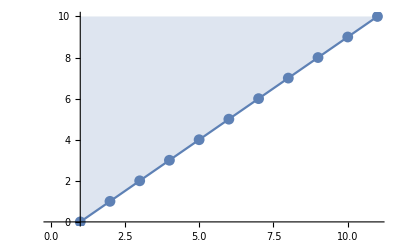

```mathematica
data=Table[i,{i,0,10}]
ListLinePlot[data,Mesh->All,Filling->Top,AxesOrigin->{1,0}]
```

```mathematica
Manipulate[lplot[{data1,data},Mesh->Full,Filling->Axis],{lplot,{ListPlot,ListLinePlot,ListLogPlot,ListLogLogPlot}},Initialization:> (data1={1,4,9,16,25})]
```

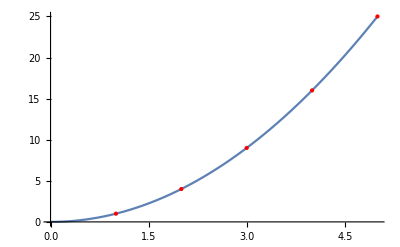

```mathematica
Show[Plot[x^2,{x,0,5}],ListPlot[Table[i^2,{i,1,5,1}],PlotStyle->{Red,PointSize[Large]}]]
```

Visualizing 2D data

```mathematica
dataset1={{1,1},{2,2},{3,3},{4,4},{5,5}};
dataset2 = Table[{i,i^2},{i,1,5}];
dataset3 = Table[{i,i^3},{i,1,5}];
```

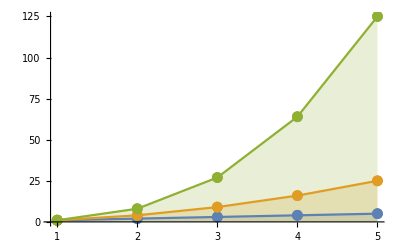

```mathematica
ListLinePlot[{dataset1,dataset2,dataset3},Mesh->Full,Filling->Bottom,PlotRange->Full]
```

```mathematica
Manipulate[ListLinePlot[Table[{n,Prime[n]},{n,1,max,1}],PlotRange->{{0,50},{0,250}}],{max,1,50,1}]
```

Visualize 3D Data

```mathematica
data3D = Table[N[Sin[x]Cos[y]],{x,0,5,0.1},{y,0,5,0.1}];
data3D = Table[i-n,{i,0,5,0.1},{n,0,3,0.1}];
```

```mathematica
ListPlot3D[data3D]
ListPointPlot3D[data3D]
```

-Graphics3D-

-Graphics3D-

Visualize a Matrix

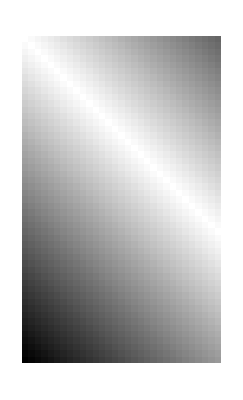

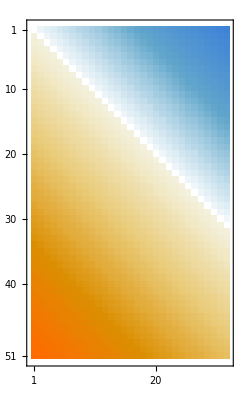

```mathematica
ArrayPlot[data3D]
MatrixPlot[data3D]
```

```mathematica
GeoGraphics[{Point[GeoPosition[{39.5,119}]],Point[GeoPosition[{40,119}]],Point[GeoPosition[{39.5,118.5}]]}]
```

-Graphics-

Visualize data with Charts

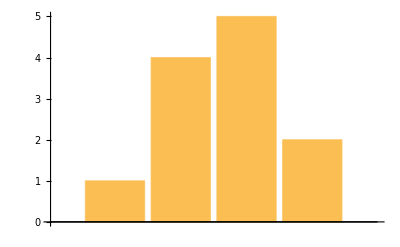

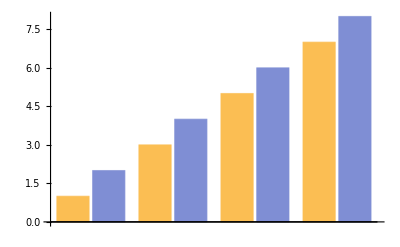

```mathematica
BarChart[{1,4,5,2}]
BarChart[{{1,2},{3,4},{5,6},{7,8}}]
```

```mathematica
Manipulate[function[{{1,2},{3,4},{5,6},{7,8}}],{function,{PieChart,PieChart3D,SectorChart,BarChart,BarChart3D}}]
```

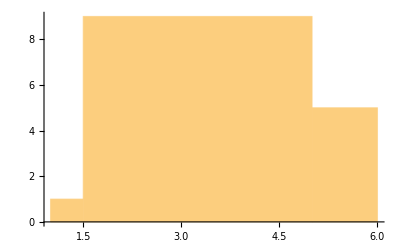

```mathematica
Histogram[{1,2,2,3,3,3,4,4,4,4,5,5,5,5,5},{{1,1.5,5,6}}]
```

```mathematica
cloudNum = RandomInteger[{1,100},{1000}];
```

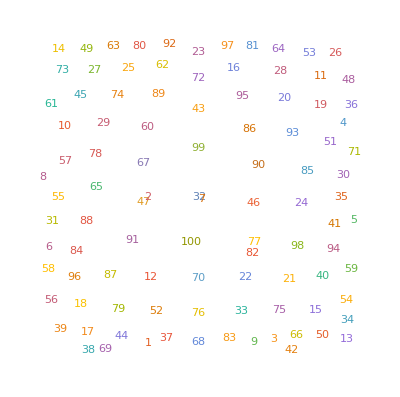

```mathematica
WordCloud[cloudNum]
```

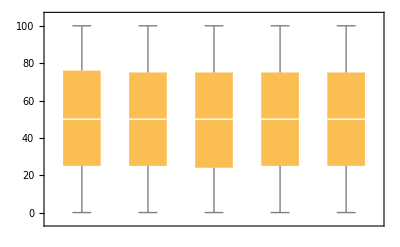

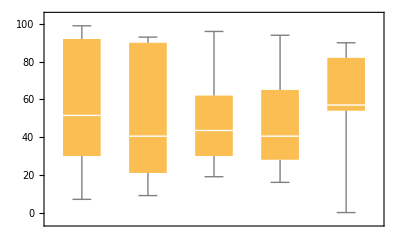

```mathematica
BoxWhiskerChart[RandomInteger[{0,100},{5,100000}]]
BoxWhiskerChart[RandomInteger[{0,100},{5,10}]]
```

```mathematica
ClearAll["Global`*"]
```